```mathematica
(* Define the sample space and probabilities *)
sampleSpace=Import["square_names_2.txt", "list"]
probabilities=Import["square_percentages_2.txt", "list"]
```

{Go,Mediterranean Avenue,Community Chest 1,Baltic Avenue,Income Tax,Reading Railroad,Oriental Avenue,Chance 1,Vermont Avenue,Connecticut Avenue,Jail / Just Visiting,St. Charles Place,Electric Company,States Avenue,Virginia Avenue,Pennsylvania Railroad,St. James Place,Community Chest 2,Tennessee Avenue,New York Avenue,Free Parking,Kentucky Avenue,Chance 2,Indiana Avenue,Illinois Avenue,B. & O. Railroad,Atlantic Avenue,Ventnor Avenue,Water Works,Marvin Gardens,Go to Jail,Pacific Avenue,North Carolina Avenue,Community Chest 3,Pennsylvania Avenue,Short Line,Chance 3,Park Place,Luxury Tax,Boardwalk}

{0.0153969,0.0156845,0.0175326,0.0192568,0.0209843,0.0229317,0.0251769,0.0267978,0.0254167,0.0238093,0.0522203,0.0221198,0.0234555,0.0247209,0.0272878,0.0310248,0.0340129,0.0372497,0.0360959,0.0342042,0.0324749,0.0305941,0.028514,0.026512,0.0252636,0.0259071,0.0260696,0.0258957,0.0252392,0.024619,0.,0.0256962,0.0247243,0.0240609,0.0234622,0.0223435,0.0204183,0.0185351,0.0176853,0.0166057}

```mathematica
(*top five names and probs*)
topfivenames={}
topfiveprobs={}
max=First[First[Position[probabilities,Max[probabilities]]]]
topfivenames=Append[topfivenames,Part[sampleSpace,max]]
topfiveprobs=Append[topfiveprobs,Part[probabilities,max]]
probabilities=Delete[probabilities,max];
sampleSpace=Delete[sampleSpace,max];

max=First[First[Position[probabilities,Max[probabilities]]]]
topfivenames=Append[topfivenames,Part[sampleSpace,max]]
topfiveprobs=Append[topfiveprobs,Part[probabilities,max]]
probabilities=Delete[probabilities,max];
sampleSpace=Delete[sampleSpace,max];

max=First[First[Position[probabilities,Max[probabilities]]]]
topfivenames=Append[topfivenames,Part[sampleSpace,max]]
topfiveprobs=Append[topfiveprobs,Part[probabilities,max]]
probabilities=Delete[probabilities,max];
sampleSpace=Delete[sampleSpace,max];

max=First[First[Position[probabilities,Max[probabilities]]]]
topfivenames=Append[topfivenames,Part[sampleSpace,max]]
topfiveprobs=Append[topfiveprobs,Part[probabilities,max]]
probabilities=Delete[probabilities,max];
sampleSpace=Delete[sampleSpace,max];

max=First[First[Position[probabilities,Max[probabilities]]]]
(*topfive=Append[topfive,{Part[sampleSpace,max], Part[probabilities, max]}];*)
topfivenames=Append[topfivenames,Part[sampleSpace,max]]
topfiveprobs=Append[topfiveprobs,Part[probabilities,max]]
probabilities=Delete[probabilities,max];
sampleSpace=Delete[sampleSpace,max];

(*bottom five names and probs*)
bottomfivenames={}
bottomfiveprobs={}
min=First[First[Position[probabilities,Min[probabilities]]]]
bottomfivenames=Append[bottomfivenames,Part[sampleSpace,min]]
bottomfiveprobs=Append[bottomfiveprobs,Part[probabilities,min]]
probabilities=Delete[probabilities,min];
sampleSpace=Delete[sampleSpace,min];

min=First[First[Position[probabilities,Min[probabilities]]]]
bottomfivenames=Append[bottomfivenames,Part[sampleSpace,min]]
bottomfiveprobs=Append[bottomfiveprobs,Part[probabilities,min]]
probabilities=Delete[probabilities,min];
sampleSpace=Delete[sampleSpace,min];

min=First[First[Position[probabilities,Min[probabilities]]]]
bottomfivenames=Append[bottomfivenames,Part[sampleSpace,min]]
bottomfiveprobs=Append[bottomfiveprobs,Part[probabilities,min]]
probabilities=Delete[probabilities,min];
sampleSpace=Delete[sampleSpace,min];

min=First[First[Position[probabilities,Min[probabilities]]]]
bottomfivenames=Append[bottomfivenames,Part[sampleSpace,min]]
bottomfiveprobs=Append[bottomfiveprobs,Part[probabilities,min]]
probabilities=Delete[probabilities,min];
sampleSpace=Delete[sampleSpace,min];

min=First[First[Position[probabilities,Min[probabilities]]]]
bottomfivenames=Append[bottomfivenames,Part[sampleSpace,min]]
bottomfiveprobs=Append[bottomfiveprobs,Part[probabilities,min]]
probabilities=Delete[probabilities,min];
sampleSpace=Delete[sampleSpace,min];

bottomfivenames = Reverse[bottomfivenames]
bottomfiveprobs = Reverse[bottomfiveprobs]
```

{}

{}

11

{Jail / Just Visiting}

{0.0522203}

17

{Jail / Just Visiting,Community Chest 2}

{0.0522203,0.0372497}

17

{Jail / Just Visiting,Community Chest 2,Tennessee Avenue}

{0.0522203,0.0372497,0.0360959}

17

{Jail / Just Visiting,Community Chest 2,Tennessee Avenue,New York Avenue}

{0.0522203,0.0372497,0.0360959,0.0342042}

16

{Jail / Just Visiting,Community Chest 2,Tennessee Avenue,New York Avenue,St. James Place}

{0.0522203,0.0372497,0.0360959,0.0342042,0.0340129}

{}

{}

26

{Go to Jail}

{0.}

1

{Go to Jail,Go}

{0.,0.0153969}

1

{Go to Jail,Go,Mediterranean Avenue}

{0.,0.0153969,0.0156845}

32

{Go to Jail,Go,Mediterranean Avenue,Boardwalk}

{0.,0.0153969,0.0156845,0.0166057}

1

{Go to Jail,Go,Mediterranean Avenue,Boardwalk,Community Chest 1}

{0.,0.0153969,0.0156845,0.0166057,0.0175326}

{Community Chest 1,Boardwalk,Mediterranean Avenue,Go,Go to Jail}

{0.0175326,0.0166057,0.0156845,0.0153969,0.}

{}

0

Delete::psl: Position specification 8 Chance 1 in {0.024391,0.0244577,0.0246284,0.0248225,0.0250736,0.0254185,0.0256284,0.0258721,0.02582,0.0256523,«30»} is not a machine-sized integer or a list of machine-sized integers.

Delete::psl: Position specification 8 Chance 1 in {Go,Mediterranean Avenue,Community Chest 1,Baltic Avenue,Income Tax,Reading Railroad,Oriental Avenue,Chance 1,Vermont Avenue,Connecticut Avenue,«30»} is not a machine-sized integer or a list of machine-sized integers.

Part::pkspec1: The expression {{8 Chance 1,0.206977}} cannot be used as a part specification.

Delete::psl: Position specification 8 {Go,Mediterranean Avenue,Community Chest 1,Baltic Avenue,Income Tax,Reading Railroad,Oriental Avenue,Chance 1,Vermont Avenue,Connecticut Avenue,«30»}⟦{{8 Chance 1,0.206977}}⟧ in {0.024391,0.0244577,0.0246284,0.0248225,0.0250736,0.0254185,0.0256284,0.0258721,0.02582,0.0256523,«30»} is not a machine-sized integer or a list of machine-sized integers.

General::stop: Further output of Delete::psl will be suppressed during this calculation.

Part::pkspec1: The expression {{8 {Go,Mediterranean Avenue,Community Chest 1,Baltic Avenue,Income Tax,Reading Railroad,Oriental Avenue,Chance 1,Vermont Avenue,Connecticut Avenue,«30»}⟦{{8 Chance 1,0.206977}}⟧,8 {0.024391,0.0244577,0.0246284,0.0248225,«4»,0.02582,0.0256523,«30»}⟦{«1»}⟧}} cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

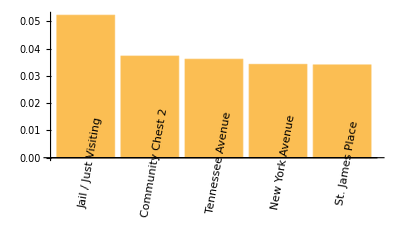

```mathematica
BarChart[topfiveprobs, ChartLabels ->Placed[topfivenames, Below, Rotate[#, 80 Degree] &]]
```

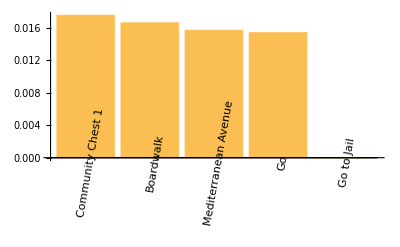

```mathematica
BarChart[bottomfiveprobs, ChartLabels ->Placed[bottomfivenames, Below, Rotate[#, 80 Degree] &]]
```

```mathematica
bottomfivenames
```

{Go to Jail,Go,Mediterranean Avenue,Boardwalk,Community Chest 1}

```mathematica
bottomfiveprobs
```

{0.,0.0153969,0.0156845,0.0166057,0.0175326}